Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

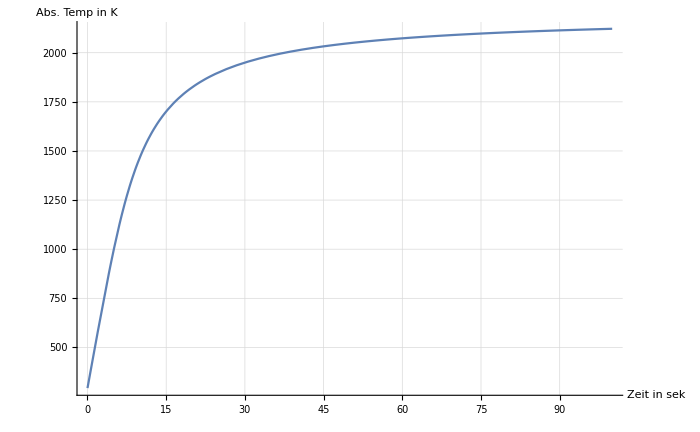

```mathematica
l=0.03;
h=0.02;
b=0.002;
Subscript[c, sp]=477;
ϵ=0.36;
ρ=7860;
σ=5.67*10^-8;
m=l*b*h*ρ;
A=2*(b*h+b*l+l*h);
η[T_]=0.972;
Subscript[P, Spule]=680.3;
Subscript[P, AB][T_]=ϵ*σ*A*((293.15+T)^4-(293.15)^4);
sol=Solve[T==Integrate[(Subscript[P, Spule]*η[T]-Subscript[P, AB][T])/(m*Subscript[c, sp]),t],T];
T1[t_]=T/.sol[[1]];
T2[t_]=T/.sol[[2]];
T3[t_]=T/.sol[[3]];
T4[t_]=T/.sol[[4]];
Plot[T2[t]+293.15,{t,0,100},PlotRange->{{0,All},{0,All}},AxesLabel->{"Zeit in sek", "Abs. Temp in K"}, GridLines->Automatic,ImageSize->700]
```